#### Distribution Functions

```mathematica
Sflu[k_,x_,g_,h_]:=∑_(m=1)^50 m^k((m M-m)!)/(m!(m M-2 m +2)!)(x^m g^(m^2- m))/(h^(m^(2+2νf)- m))+Abs[N[∑_(m=51)^500 m^k 1/(√(2π)m^(5/2))(√(M-1))/(M-2)^(5/2)((x/xc)^m g^(m^2- m))/(h^(m^(2+2νf)- m))]];mweight[power_,x_,g_,h_]:=Sflu[1+power,x,g,h]/Sflu[1,x,g,h];
gf[Δ2χ_,x_,g_,h_]:=Exp[(M ϕc)^(d/2)(mweight[1,x,g,h])^(d-1)/(mweight[1+2νf,x,g,h])^(d/2)(Δ2χ^(d ν)-Δ2χ^(d ν-1)ν/((M ϕc)mweight[1,x,g,h]))];
hf[Δ2χ_,x_,g_,h_]:=Exp[(M ϕc)^(d/2)Δ2χ^(d ν)/2(mweight[1,x,g,h])^d/(mweight[1+2νf,x,g,h])^(d/2+1)];
```

#### Import data and input parameters

```mathematica
Δ2χxghcr=Import["/Users/siao-fongli/Projects/PolydipolesGels/Δ2χxghcr_phi_th_020.dat"];
Δ2χxghcr[[;;,5]](*Check Accuracy*)
Δ2Χ=Δ2χxghcr[[;;,1]];
X=Δ2χxghcr[[;;,2]];
G=Δ2χxghcr[[;;,3]];
H=Δ2χxghcr[[;;,4]];
```

{1.,1.,1.,1.00001,1.00001,1.,0.999999,0.999998,0.999997,0.999995,0.999992,1.,1.,1.,1.00001,1.00001,0.999998,0.999996,0.999994,0.999991,1.,1.}

```mathematica
(*RG parameters*)
d=3;
ν=0.63;
η=0.04;
νf=1/2;
M=100;(*degree of polymerization*)
xc=N[(M-2)^(M-2)/(M-1)^(M-1)];
ϕth=0.20(*1/(√(M+(3 M^2+M^2/(M-1))/((M-1)^2-1))+1)*);(*gelation concentration*)
Keq=1/ϕth(M-1)/(M-2)^2;
α[ϕc_]:=1+1/(2(ϕc/ϕth)((M-1)/(M-2)^2))-√((1+1/(2(ϕc/ϕth)((M-1)/(M-2)^2)))^2-1);(*reaction rate*)
ϕc=x/.FindRoot[x-1/(1+√(M+3 M^2(α[x])^2(1+α[x]/3)/(1+3α[x]-(M-1)(α[x])^2(α[x]+3))))==0,{x,1/(√M+1)}];
(*To get χASc*)
Quiet[x0=x/.FindRoot[Sflu[1,x,1,1]==Keq ϕc/M,{x,0.0035}]];
χASc=1/2(1/(1-ϕc)+1/(M ϕc mweight[1,x0,1,1]));
```

```mathematica
ϕc
N[ϕth]
Tc=y/.FindRoot[χeff[y]==χASc,{y,1}];
Tc
Exp[-θp/Tc]Keq(*Exp[Δs/Subscript[k, B]]*)
```

0.0903001

0.13

1.52374

0.0484703

#### Weight Distribution Function

```mathematica
θp=210/280;
χeff[T_]:=(1/2+1/(√M)+1/(2M))1/T+(4π)/18 θp^2/T^2;
Tc=y/.FindRoot[χeff[y]==χASc,{y,1}];
T={};
Quiet[Do[T=Append[T,y/.FindRoot[1/(1-ϕc)+1/(M ϕc mweight[1,X[[n]],G[[n]],H[[n]]])-2χeff[y]==Δ2Χ[[n]],{y,1}]],{n,Length[Δ2Χ]}]
];
```

```mathematica
Keq;
KT=Exp[θp/T]Exp[-θp/Tc]Keq;(*Equilibrium Constant at Difernet Temperature*)
Kϕ1={};
Quiet[Do[Kϕ1=Append[Kϕ1,x/.FindRoot[Sflu[1,x,1,1]==KT[[n]] ϕc/M,{x,0.0035}]],{n,Length[KT]}]
];
W1={};(*Weight Fractions of single chains*)
Do[W1=Append[W1, Kϕ1[[n]]/(KT[[n]]ϕc)],{n,Length[KT]}];
W1Flu={};
Do[W1Flu=Append[W1Flu, X[[n]]/(KT[[n]]ϕc)],{n,Length[KT]}];
```

```mathematica
Export["/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_013.dat",Transpose@{(1/Tc-1/T)^-1,W1,W1Flu},"Table"]
```

/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_013.dat

#### Drawing Weight Distributions

```mathematica
TWWF20=Import["/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_020.dat"];
TWWF16=Import["/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_016.dat"];
TWWF13=Import["/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_013.dat"];
```

```mathematica
Tre20=TWWF20[[;;,1]];
W120=TWWF20[[;;,2]];
W1FLu20=TWWF20[[;;,3]];
Tre16=TWWF16[[;;,1]];
W116=TWWF16[[;;,2]];
W1FLu16=TWWF16[[;;,3]];
Tre13=TWWF13[[;;,1]];
W113=TWWF13[[;;,2]];
W1FLu13=TWWF13[[;;,3]];
```

```mathematica
ticks={#,ToString[PercentForm[#]]}&/@Range[0.5,0.8,0.01];
```

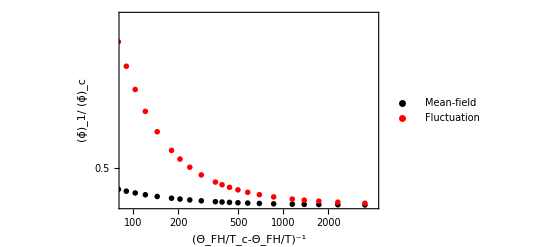

```mathematica
Show[
ListLogLogPlot[{Transpose@{Tre13,W113},Transpose@{Tre13,W1FLu13}},AxesOrigin->{Automatic,1},Frame->True,FrameLabel->{Style["(Θ_FH/T_c-Θ_FH/T)^-1",12],Style["(ϕ̄)_1/ (ϕ̄)_c ",12]},
LabelStyle->Directive[FontFamily->"Times New Roman"],
FrameTicks->{{ticks,Automatic},Automatic},
PlotRange->{{87,4000},Automatic},PlotStyle->{Directive[Black,PointSize[Large]],Directive[Red,PointSize[Large]]},PlotMarkers->"OpenMarkers",PlotLegends->Placed[{"Mean-field","Fluctuation"},{Right,Top}]]
]
```

```mathematica
Export["/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_013.pdf",%]
```

/Users/siao-fongli/Projects/PolydipolesGels/W1_phi_th_013.pdf

#### Temperature T and Correlation Length ξ

```mathematica
(*Tempratue*)
(*Given UCST and dipole strength*)
θp=210/280;
χeff[T_]:=(1/2+1/(√M)+1/(2M))1/T+(4π)/18 θp^2/T^2;
Tc=y/.FindRoot[χeff[y]==χASc,{y,1}];
T={};
Quiet[Do[T=Append[T,y/.FindRoot[1/(1-ϕc)+1/(M ϕc mweight[1,X[[n]],G[[n]],H[[n]]])-2χeff[y]==Δ2Χ[[n]],{y,1}]],{n,Length[Δ2Χ]}]
];
(*Corrleation Length*)
ξ[Δ2χ_,x_,g_,h_]:=1/Δ2χ^ν √(1/(3 M ϕc)mweight[1+2νf,x,g,h]/(mweight[1,x,g,h])^2);
isca[Δ2χ_,x_,g_,h_]:=Δ2χ^(-(2-η)ν)(1/(3 M ϕc)mweight[1+2νf,x,g,h]/(mweight[1,x,g,h])^2)^(-η/2);
Q={};
Quiet[Do[Q=Append[Q,1/(3 M ϕc)mweight[1+2νf,X[[n]],G[[n]],H[[n]]]/(mweight[1,X[[n]],G[[n]],H[[n]]])^2],{n,Length[Δ2Χ]}]]
Ξ={};
Quiet[Do[Ξ=Append[Ξ,ξ[Δ2Χ[[n]],X[[n]],G[[n]],H[[n]]]],{n,Length[Δ2Χ]}]]
Isca={};
Quiet[Do[Isca=Append[Isca,isca[Δ2Χ[[n]],X[[n]],G[[n]],H[[n]]]],{n,Length[Δ2Χ]}]]
```

```mathematica
mweight[1,x0,1,1]
Quiet[mweight[1,X,G,H]]
```

1.85443

{1.84498,1.84075,1.8366,1.83251,1.82845,1.82038,1.81239,1.80445,1.79657,1.78873,1.78094,1.77322,1.75415,1.73548,1.71724,1.69946,1.66526,1.63293,1.60241,1.57361,1.54646,1.52081}

FittedModel[-1.40428+1.02425 x]

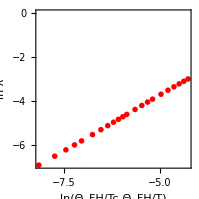

```mathematica
fitRange=Flatten[Position[(1/Tc-1/T)^-1,x_/;x<500&&x>100]];
fit=LinearModelFit[Transpose@{Log[((1/Tc-1/T)^-1)[[fitRange]]],Log[(1/Δ2Χ)[[fitRange]]]},x,x]
(*fit=LinearModelFit[Transpose@{Log[1/Δ2Χ],Log[(1/Tc-1/T)^-1]},x,x]*)
fit[{"BestFit","RSquared","FitResiduals","ParameterTable"}];
ListPlot[Transpose@{Log[(1/Tc-1/T)],Log[Δ2Χ/1]},Frame->True,FrameLabel->{"ln(Θ_FH/Tc-Θ_FH/T)","ln λ"},AspectRatio->1,PlotRange->All,PlotStyle->Directive[Red,PointSize[Large]],PlotMarkers->"OpenMarkers"]
```

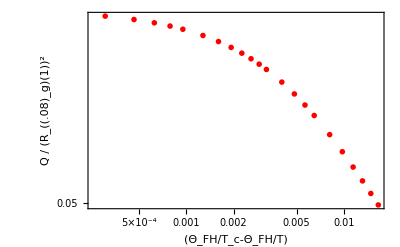

/Users/siao-fongli/Projects/PolydipolesGels/QT_phi_th_020.pdf

```mathematica
ListLogLogPlot[{Transpose@{(1/Tc-1/T),Q}},AxesOrigin->{Automatic,1},Frame->True,FrameLabel->{Style["(Θ_FH/T_c-Θ_FH/T)",12],Style["Q / (R_((.08)_g)(1))^2",12]},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotStyle->Directive[Red,PointSize[Large]],PlotMarkers->"OpenMarkers"]
Export["/Users/siao-fongli/Projects/PolydipolesGels/QT_phi_th_020.pdf",%]
```

FittedModel[-0.942722+0.970955 x]

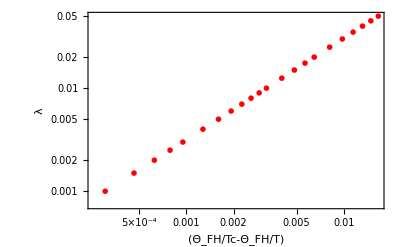

```mathematica
fitRange=Flatten[Position[(1/Tc-1/T)^-1,x_/;x<4000&&x>1000]];
fit=LinearModelFit[Transpose@{Log[((1/Tc-1/T)^-1)[[fitRange]]],Log[(1/Δ2Χ)[[fitRange]]]},x,x]
fit[{"BestFit","RSquared","FitResiduals","ParameterTable"}];
Show[ListLogLogPlot[Transpose@{(1/Tc-1/T),(1/Δ2Χ)^-1},Frame->True,FrameLabel->{Style["(Θ_FH/Tc-Θ_FH/T)",12],Style["λ",12]},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotRange->All,PlotStyle->Directive[Red,PointSize[Large]],PlotMarkers->"OpenMarkers"],
LogLogPlot[{Exp[fit[Log[x]]]},{x,Min[((1/Tc-1/T)^-1)[[fitRange]]],Max[((1/Tc-1/T)^-1)[[fitRange]]]},PlotStyle->{Dashed,Black}]]
(*Export["/Users/siao-fongli/Projects/PolydipolesGels/LT_phi_th_020.pdf",%]*)
```

FittedModel[-2.38867+0.678829 x]

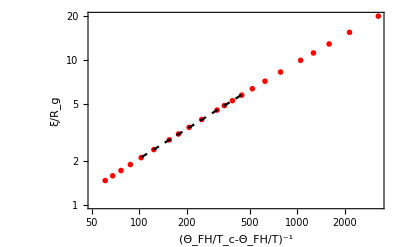

```mathematica
fitRange=Flatten[Position[(1/Tc-1/T)^-1,x_/;x<500&&x>100]];
fit=LinearModelFit[Transpose@{Log[((1/Tc-1/T)^-1)[[fitRange]]],Log[Ξ[[fitRange]]]},x,x]
fit[{"BestFit","RSquared","FitResiduals","ParameterTable"}];
Show[ListLogLogPlot[{Transpose@{(1/Tc-1/T)^-1,Ξ}},AxesOrigin->{Automatic,1},Frame->True,FrameLabel->{"(Θ_FH/T_c-Θ_FH/T)^-1","ξ/R_g "},PlotStyle->Directive[Red,PointSize[Large]],PlotMarkers->"OpenMarkers"],
LogLogPlot[{Exp[fit[Log[x]]]},{x,Min[((1/Tc-1/T)^-1)[[fitRange]]],Max[((1/Tc-1/T)^-1)[[fitRange]]]},PlotStyle->{Dashed,Black}]]
```

FittedModel[-1.29197+1.22599 x]

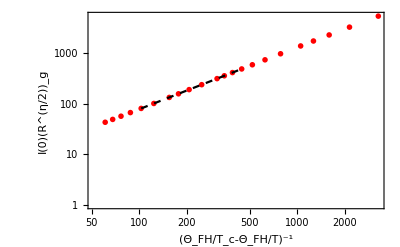

```mathematica
fitRange=Flatten[Position[(1/Tc-1/T)^-1,x_/;x<500&&x>100]];
fit=LinearModelFit[Transpose@{Log[((1/Tc-1/T)^-1)[[fitRange]]],Log[Isca[[fitRange]]]},x,x]
fit[{"BestFit","RSquared","FitResiduals","ParameterTable"}];
Show[
ListLogLogPlot[{Transpose@{(1/Tc-1/T)^-1,Isca}},AxesOrigin->{Automatic,1},Frame->True,FrameLabel->{"(Θ_FH/T_c-Θ_FH/T)^-1","I(0)(R^(η/2))_g "},PlotStyle->Directive[Red,PointSize[Large]],PlotMarkers->"OpenMarkers"],
LogLogPlot[{Exp[fit[Log[x]]]},{x,Min[((1/Tc-1/T)^-1)[[fitRange]]],Max[((1/Tc-1/T)^-1)[[fitRange]]]},PlotStyle->{Dashed,Black}]]
```

#### Record critical exponent at different ϕth

```mathematica
Φth={0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.20};
Keqlist=1/Φth(M-1)/(M-2)^2;
Λlist={1.02425,1.01696,1.00981,1.00470,1.00097,0.998181,0.996115,0.99456};
Νlist={0.77551,0.74621,0.726739,0.712171,0.700907,0.691968,0.684757,0.678829};
Γlist={1.25955,1.25152,1.24329,1.23744,1.23318,1.23003,1.22771,1.22599};
```

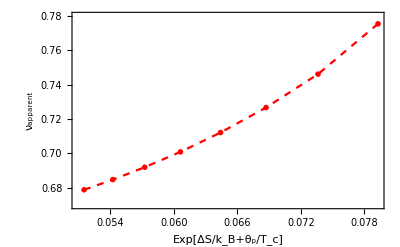

/Users/siao-fongli/Projects/PolydipolesGels/nu.pdf

```mathematica
upperTicks=Transpose@{Keqlist,Φth};
ListPlot[Transpose@{Keqlist,Νlist},Joined->True,PlotStyle->Directive[Red,PointSize[Large],Dashed],PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{{Style["ν_apparent",12],""},{Style["Exp[ΔS/k_B+θ_p/T_c]",12],Style["ϕ_th",12]}},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotRange->{0.67,0.78},FrameTicks->{{Automatic,Automatic},{Automatic,upperTicks}}]
Export["/Users/siao-fongli/Projects/PolydipolesGels/nu.pdf",%]
```

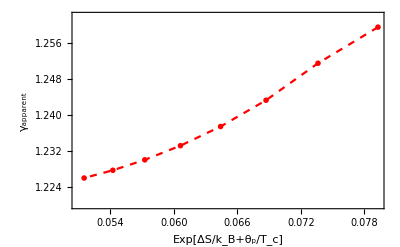

/Users/siao-fongli/Projects/PolydipolesGels/gamma.pdf

```mathematica
upperTicks=Transpose@{Keqlist,Φth};
ListPlot[Transpose@{Keqlist,Γlist},Joined->True,PlotStyle->Directive[Red,PointSize[Large],Dashed],PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{{Style["γ_apparent",12],""},{Style["Exp[ΔS/k_B+θ_p/T_c]",12],Style["ϕ_th",12]}},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotRange->{1.22,1.262},FrameTicks->{{Automatic,Automatic},{Automatic,upperTicks}}]
Export["/Users/siao-fongli/Projects/PolydipolesGels/gamma.pdf",%]
```

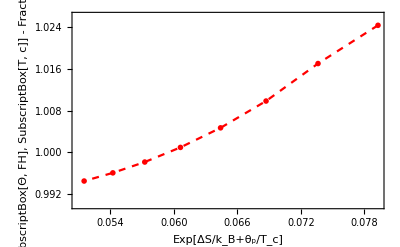

/Users/siao-fongli/Projects/PolydipolesGels/lambda.pdf

```mathematica
upperTicks=Transpose@{Keqlist,Φth};
ListPlot[Transpose@{Keqlist,Λlist},Joined->True,PlotStyle->Directive[Red,PointSize[Large],Dashed],PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{{Style["(d lnλ)/(d ln (FractionBox[SubscriptBox[Θ, FH], SubscriptBox[T, c]] - FractionBox[SubscriptBox[Θ, FH], T]))",12],""},{Style["Exp[ΔS/k_B+θ_p/T_c]",12],Style["ϕ_th",12]}},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotRange->{0.99,1.026},FrameTicks->{{Automatic,Automatic},{Automatic,upperTicks}}]
Export["/Users/siao-fongli/Projects/PolydipolesGels/lambda.pdf",%]
```